# Domača Naloga 2

## Naloga 1

```mathematica
d=Daljica[{-1, 1},{3, -1}]
d2=Daljica[{-1, -1},{3, 1}]
```

Daljica[{-1,1},{3,-1}]

Daljica[{-1,-1},{3,1}]

```mathematica
ClearAll
```

```mathematica
Dolzina[Daljica[AA_, BB_]]:=Norm[BB-AA]
```

```mathematica
Dolzina[d]
```

2 √5

Dolzina[Daljica[{-1,1},{3,-1}]]

```mathematica
Slika[Daljica[AA_, BB_]]:=Line[{AA, BB}]
Slika[d]
```

Line[{{-1,1},{3,-1}}]

```mathematica
Narisi[d__Daljica]:=Graphics[Map[Slika, List[d]]]
```

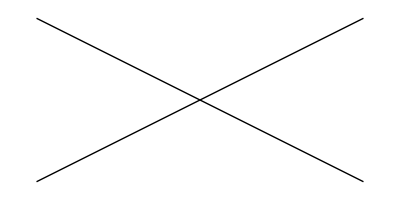

```mathematica
Narisi[d, d2]
```

```mathematica
ClearAll[x, y, EnacbaNosilke]
```

```mathematica
EnacbaNosilke[Daljica[AA_, BB_]]:=Module[{x1, y1, x2, y2},
{x1, y1}=AA;
{x2, y2}=BB;
k=(y2-y1)/(x2-x1);
n=n/.First[Solve[y1==k*x1+n, n]];
y==k*x+n
]
```

```mathematica
EnacbaNosilke[d]
```

Solve::ivar: 1/2 is not a valid variable.

ReplaceAll::reps: {True} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

y==-x/2+(1/2/.True)

## Naloga 2

```mathematica
Presek[Daljica[AA_, BB_],Daljica[CC_, DD_]]:=Module[{resitev},
resitev=Solve[{AA+r(BB-AA)==CC+s(DD-CC), r≥0, r≤1, s≥0,s≤1}, {r, s}]
]
```

```mathematica
Presek[d, d2]
```

{{r→1/2,s→1/2}}

## Naloga 3

```mathematica
m1=Mnogokotnik[{0,0},{1,1},{0,3},{-1,2}]
m2 =Append[m1,m1[[1]]]
```

Mnogokotnik[{0,0},{1,1},{0,3},{-1,2}]

Mnogokotnik[{0,0},{1,1},{0,3},{-1,2},{0,0}]

```mathematica
Slika[Mnogokotnik[t__]] := Line[{t}]
```

```mathematica
Slika[m2]
```

Line[{{0,0},{1,1},{0,3},{-1,2},{0,0}}]

```mathematica
Narisi[m__Mnogokotnik] := Graphics[Slika[m]]
```

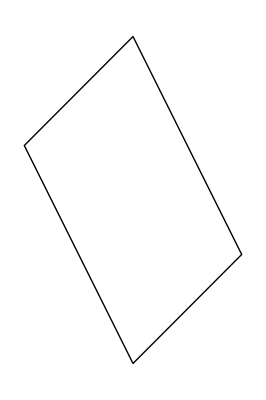

```mathematica
Narisi[m2]
```

```mathematica
PravilniNKotnik[n_,r_] :=Graphics[{Line[Table[{r*Cos[(2Pi*i)/n],r*Sin[(2Pi*i)/n]},{i,0,n}]],Point[{0,0}]}]
```

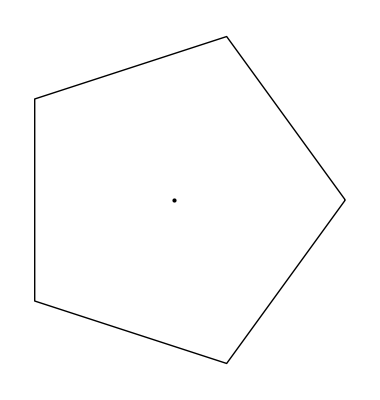

```mathematica
p5 = PravilniNKotnik[5, 2]
```

```mathematica
PravilniNKotnik2[n_,r_] := Show[Graphics[{{EdgeForm[Thick],White,RegularPolygon[{0,0},r,n]},{Point[{0,0}]}}]]
```

```mathematica
p55=PravilniNKotnik2[5, 2]
```

-Graphics-

```mathematica
PravilniNKotnik[n_,r_,phi_] := Graphics[{Line[Table[{r*Cos[(2Pi*i+phi)/n ],r*Sin[(2Pi*i+phi)/n]},{i,0,n}]],Point[{0,0}]}]
```

```mathematica
pNeki = Manipulate[PravilniNKotnik[5,2,phi],{phi,1.5,33}]
```

```mathematica
Daljice[Mnogokotnik[t__]] := Map[Daljica,Partition[{t}, 2,1]]
daljice = Daljice[m2]
```

{Daljica[{{0,0},{1,1}}],Daljica[{{1,1},{0,3}}],Daljica[{{0,3},{-1,2}}],Daljica[{{-1,2},{0,0}}]}

```mathematica
Partition[{1,2,3,4,5},2]
Partition[{1,2,3,4,5},2,1]
```

{{1,2},{3,4}}

{{1,2},{2,3},{3,4},{4,5}}

## Naloga 4

```mathematica
Presek[m_Mnogokotnik,d_Daljica] := Presek[daljice[[1]],d]
Presek[m2,d]
daljice[[1]]
```

Presek[Mnogokotnik[{0,0},{1,1},{0,3},{-1,2},{0,0}],d]

Daljica[{{0,0},{1,1}}]

```mathematica
Presek[d,Slika[d2]]
```

Presek[d,Slika[d2]]

## Naloga 5

```mathematica
VsiPari[f_,sez1_,sez2_]:=Flatten[Outer[f,sez1,sez2],1]
VsiPari[f,{1,2,3},{a,b}]
Outer[f,{1,2,3},{4,5,6}]
Flatten[{{f[1,4],f[1,5],f[1,6]},{f[2,4],f[2,5],f[2,6]},{f[3,4],f[3,5],f[3,6]}},1]
g[m1_Mnogokotnika,m2_Mnogotnika]:=Presek[m1,m2]
Presek[m1_Mnogokotnika,m2_Mnogkotnika]:=VsiPari[g,m1,m2]
```

{f[1,a],f[1,b],f[2,a],f[2,b],f[3,a],f[3,b]}

{{f[1,4],f[1,5],f[1,6]},{f[2,4],f[2,5],f[2,6]},{f[3,4],f[3,5],f[3,6]}}

{f[1,4],f[1,5],f[1,6],f[2,4],f[2,5],f[2,6],f[3,4],f[3,5],f[3,6]}

## Naloga 6

V kvadru s stranicami dolžin 1, 2, 3 izračunaj dolžino telesne diagonale.

```mathematica
s1=1
s2=2
```

```mathematica
s3=3
```

```mathematica
Diagonala[AA_, BB_, CC_]:=√(AA^2+BB^2+CC^2)
```

```mathematica
Diagonala[s1,s2,s3]
```

√14

```mathematica
Graphics3D[Cuboid[{s1, s2, s3}]]
```

-Graphics3D-